# Functions and Modules

## Functions

```mathematica
?Function
```

### One way to define a function

Defining a function in Mathematica requires that we define the parameters of the function using an underscore:

```mathematica
f[x_] := 3 + x
f[3]
```

6

```mathematica
f[y]
```

3+y

### A second way

```mathematica
Function[x, 3 +x][2]
```

5

```mathematica
Function[3 + #][2]
```

5

```mathematica
(3 + #) & [2]
```

5

### A fancy way to define a function

In the following example, we create an anonymous function and assign it to the variable f

```mathematica
f = (3 + #) &
f[2]
```

3+#1&

5

### More than one variable

Via the explicit way

```mathematica
myNorm[x_, y_] = Sqrt[x^2+y^2]
```

√(x^2+y^2)

```mathematica
myNorm[(x - ϕ), 1]
```

√(1+(x-ϕ)^2)

Via an anonymous function:

```mathematica
Sqrt[#1^2+ #2^2] & [(x - ϕ), 1]
```

√(1+(x-ϕ)^2)

### Functions with vectors

```mathematica
vectorNorm[X_] := Sqrt[X[[1]]^2+ X[[2]]^2]
vectorNorm[{1, x - ϕ}]
```

√(1+(x-ϕ)^2)

```mathematica
vectorNorm[{3, 5}]
```

√34

A more general way

```mathematica
vectorNorm[X_] := Sqrt[X . X]
vectorNorm[{1, x - ϕ, y}]
```

√(1+y^2+(x-ϕ)^2)

## Modules

```mathematica
?Module
```

Defining a module myPow that accepts a variable and returns a single result
* We first define the input parameters of the module
* The last quantity inside the module is the value that is returned

```mathematica
myModule[x0_] := Module[{x = x0}, a= 1 / x; b = Sin[a^2]]
myModule[x]
```

Sin[1/x^2]

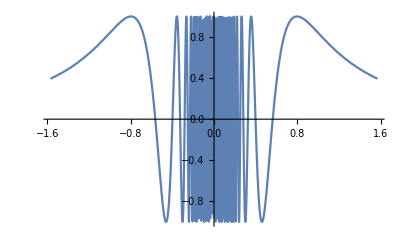

```mathematica
Plot[myModule[x], {x, -π/2, π/2}]
```

You can call a module with different parameters

```mathematica
myModule[{x, y}]
```

```mathematica
{Sin[1/x^2],Sin[1/y^2]}
```

Why did the first entry resulted in explicit form and the second in a numeric form?

```mathematica
Table[myModule[{x,y}],{x,-2 π,-0.99},{y,0.01,2 π}] // MatrixForm
```

((Sin[1/(4 π^2)]
-0.305614) | (Sin[1/(4 π^2)]
0.830662) | (Sin[1/(4 π^2)]
0.244999) | (Sin[1/(4 π^2)]
0.11015) | (Sin[1/(4 π^2)]
0.0621486) | (Sin[1/(4 π^2)]
0.0398299) | (Sin[1/(4 π^2)]
0.0276819)
(Sin[1/(1-2 π)^2]
-0.305614) | (Sin[1/(1-2 π)^2]
0.830662) | (Sin[1/(1-2 π)^2]
0.244999) | (Sin[1/(1-2 π)^2]
0.11015) | (Sin[1/(1-2 π)^2]
0.0621486) | (Sin[1/(1-2 π)^2]
0.0398299) | (Sin[1/(1-2 π)^2]
0.0276819)
(Sin[1/(2-2 π)^2]
-0.305614) | (Sin[1/(2-2 π)^2]
0.830662) | (Sin[1/(2-2 π)^2]
0.244999) | (Sin[1/(2-2 π)^2]
0.11015) | (Sin[1/(2-2 π)^2]
0.0621486) | (Sin[1/(2-2 π)^2]
0.0398299) | (Sin[1/(2-2 π)^2]
0.0276819)
(Sin[1/(3-2 π)^2]
-0.305614) | (Sin[1/(3-2 π)^2]
0.830662) | (Sin[1/(3-2 π)^2]
0.244999) | (Sin[1/(3-2 π)^2]
0.11015) | (Sin[1/(3-2 π)^2]
0.0621486) | (Sin[1/(3-2 π)^2]
0.0398299) | (Sin[1/(3-2 π)^2]
0.0276819)
(Sin[1/(4-2 π)^2]
-0.305614) | (Sin[1/(4-2 π)^2]
0.830662) | (Sin[1/(4-2 π)^2]
0.244999) | (Sin[1/(4-2 π)^2]
0.11015) | (Sin[1/(4-2 π)^2]
0.0621486) | (Sin[1/(4-2 π)^2]
0.0398299) | (Sin[1/(4-2 π)^2]
0.0276819)
(Sin[1/(5-2 π)^2]
-0.305614) | (Sin[1/(5-2 π)^2]
0.830662) | (Sin[1/(5-2 π)^2]
0.244999) | (Sin[1/(5-2 π)^2]
0.11015) | (Sin[1/(5-2 π)^2]
0.0621486) | (Sin[1/(5-2 π)^2]
0.0398299) | (Sin[1/(5-2 π)^2]
0.0276819))

A module with parts

```mathematica
myAverage[X0_] := Module[{X = X0},
nElements = Length[X];
sumElements = Total[X];
sumElements / nElements
]
z = Range[1, 100];
myAverage[z]
```

```mathematica
101/2//N
```

50.5

```mathematica
Mean[z]
```

```mathematica
101/2 //N
```

50.5

A second way to define the function

```mathematica
myAverage[X_] := Module[{nElements = Length[X],
sumElements = Total[X]},
   sumElements / nElements
]
myAverage[z]
```

101/2

```mathematica
z1 = Range[1, 100];
z2 = Range[100, 201];
myAverage[{z1, z2}]
```

How can I define myAverage so that it correctly computes the average of n>1 array of values?

```mathematica
Map[myAverage, {z1, z2}]
```

{101/2,301/2}

Does not work...

```mathematica
myAverage[{z1, z2}]
```

1/2 Total[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201}}]

### Functions with two outputs

```mathematica
polar[X_] := Module[{x1 = X[[1]], x2=X[[2]]},
coord1 = Sqrt[x1^2 + x2^2];
coord2 = ArcTan[x2/x1];
{coord1, coord2}
]
polar[{4, 3}]
```

{5,ArcTan[3/4]}

Function trickery: mapping a list to the arguments of a function

```mathematica
g[x1_, x2_] := Sqrt[x1^2+ x2^2]
g[x, y]
```

√(x^2+y^2)

```mathematica
g @@ {{x, y}, {1, 2}}
```

{√(1+x^2),√(4+y^2)}